{{-66.5,20.},{-66.5,25.5},{-66.5,31.},{-66.5,36.5},{-66.5,42.},{-66.5,47.5},{-58.,53.},{-66.5,58.5},{-58.5,64.},{-58.5,69.5},{-50.,75.}}

{{-108.5,75.},{-100.,84.},{-91.5,94.},{-90.,103.},{-82.,109.}}

{{-50.,13.},{-58.5,18.},{-50.,18.},{-41.5,18.}}

{{-66.5,20.},{-66.5,25.5},{-66.5,31.},{-66.5,36.5},{-66.5,42.},{-66.5,47.5},{-58.,53.},{-66.5,58.5},{-58.5,64.},{-58.5,69.5},{-50.,75.},{-108.5,75.},{-100.,84.},{-91.5,94.},{-90.,103.},{-82.,109.},{-50.,13.},{-58.5,18.},{-50.,18.},{-41.5,18.}}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 206.257 | 42.0684 | 4.9029 | 0.000844266
x | 2.52908 | 0.667712 | 3.78768 | 0.00429798

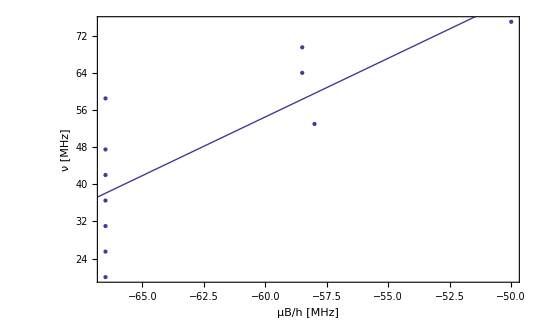

| Estimate | Standard Error | t-Statistic | P-Value
1 | 218.997 | 14.4254 | 15.1814 | 0.000620577
x | 1.33471 | 0.15211 | 8.77465 | 0.00311774

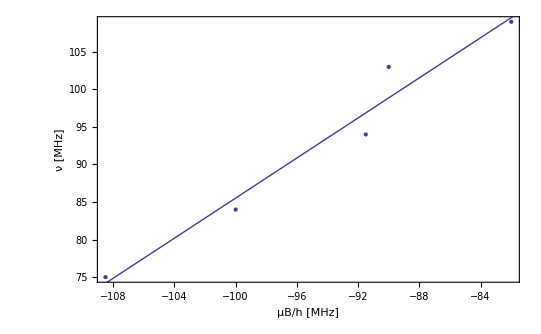

| Estimate | Standard Error | t-Statistic | P-Value
1 | 16.75 | 12.8274 | 1.3058 | 0.321615
x | -2.82186×10^-16 | 0.254713 | -1.10786×10^-15 | 1.

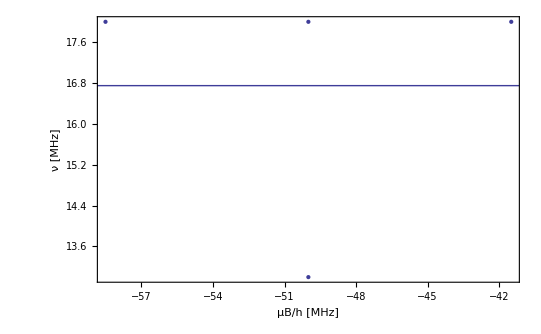

| Estimate | Standard Error | t-Statistic | P-Value
1 | -25.6011 | 21.2691 | -1.20368 | 0.244305
x | -1.14974 | 0.302646 | -3.79896 | 0.00131443

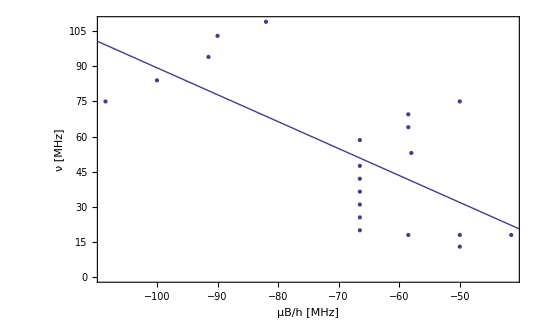

```mathematica
Needs["ErrorBarPlots`"]

mittlere={{20,133,-266},{25.5,183,-316},{31,233,-366},{36.5,283,-416},{42,333,-466},{47.5,400,-533},{53,450,-566},{58.5,500,-633},{64,566,-683},{69.5,616,-733},{75,683,-783}};
kleine={{75,616,-833},{84,700,-900},{94,800,-983},{103,900,-1080},{109,966,-1130}};
grosse={{13,66,-166},{18,116,-233},{18,183,-283},{18,250,-333}};

mittlerem={};
kleinem={};
grossem={};

For[i=1,i<=Length[mittlere],i++,AppendTo[mittlerem,{(mittlere[[i]][[2]]+mittlere[[i]][[3]])/2,mittlere[[i]][[1]]}]];

For[i=1,i<=Length[kleine],i++,AppendTo[kleinem,{(kleine[[i]][[2]]+kleine[[i]][[3]])/2,kleine[[i]][[1]]}]];

For[i=1,i<=Length[grosse],i++,AppendTo[grossem,{(grosse[[i]][[2]]+grosse[[i]][[3]])/2,grosse[[i]][[1]]}]];

kombiniert=Join[mittlerem,kleinem,grossem];

N[mittlerem]
N[kleinem]
N[grossem]
N[kombiniert]

mittlerefit=LinearModelFit[mittlerem,x,x];
kleinefit=LinearModelFit[kleinem,x,x];
grossefit=LinearModelFit[grossem,x,x];
kombiniertfit=LinearModelFit[kombiniert,x,x];

mittlerefit["ParameterTable"]
Show[ListPlot[mittlerem],Plot[mittlerefit[x],{x,-70,-50}],Axes->False,Frame->{True,True,False,False},FrameLabel->{"μB/h [MHz]","ν [MHz]"}]
kleinefit["ParameterTable"]
Show[ListPlot[kleinem],Plot[kleinefit[x],{x,-110,-80}],Axes->False,Frame->{True,True,False,False},FrameLabel->{"μB/h [MHz]","ν [MHz]"}]
grossefit["ParameterTable"]
Show[ListPlot[grossem],Plot[grossefit[x],{x,-60,-40}],Axes->False,Frame->{True,True,False,False},FrameLabel->{"μB/h [MHz]","ν [MHz]"}]
kombiniertfit["ParameterTable"]
Show[ListPlot[kombiniert],Plot[kombiniertfit[x],{x,-110,-40}],Axes->False,Frame->{True,True,False,False},FrameLabel->{"μB/h [MHz]","ν [MHz]"}]
```